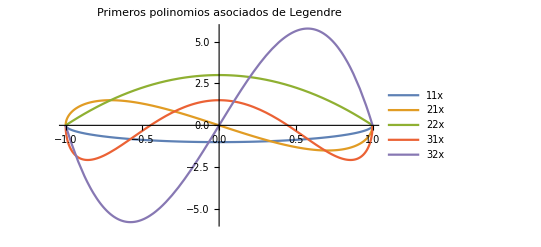

```mathematica
Plot[{LegendreP[1,1,x], LegendreP[2,1,x],LegendreP[2,2,x], LegendreP[3,1,x] , LegendreP[3,2,x]},{x,-1,1},PlotLabel->"Primeros polinomios asociados de Legendre", PlotLegends->"Expressions"]
```

```mathematica
SphericalPlot3D[SphericalHarmonicY[0,0,θ,φ],{θ,0,Pi},{ϕ,0,2 Pi}, PlotLabel->"Armónico esférico Y_00  (θ, ϕ)]"]
```

-Graphics3D-

```mathematica
Y10 = SphericalHarmonicY[1,0,θ,ϕ]
```

1/2 √(3/π) Cos[θ]

```mathematica
SphericalPlot3D[Abs[Re[Y10]],{θ,0, Pi},{ϕ,0,2 Pi}, PlotLabel->"Armónico esférico Y_10  (θ, ϕ)]",PlotStyle->{Red,Opacity[0.75]}]
```

-Graphics3D-

```mathematica
Y11 = SphericalHarmonicY[1,1,θ,ϕ]
```

-1/2 ⅇ^(ⅈ ϕ) √(3/(2 π)) Sin[θ]

```mathematica
SphericalPlot3D[Abs[Re[Y11]],{θ,0, Pi},{ϕ,0,2 Pi}, PlotLabel->"Armónico esférico Y_11  (θ, ϕ)]",PlotStyle->{Gray,Opacity[0.75]}]
```

-Graphics3D-

```mathematica
Y20 = SphericalHarmonicY[2,0,θ,ϕ]
```

1/4 √(5/π) (-1+3 Cos[θ]^2)

```mathematica
SphericalPlot3D[Abs[Re[Y20]],{θ,0, Pi},{ϕ,0,2 Pi}, PlotLabel->"Armónico esférico Y_20  (θ, ϕ)]",PlotStyle->{Pink,Opacity[0.75]}]
```

-Graphics3D-

```mathematica
Y21 = SphericalHarmonicY[2,1,θ,ϕ]
```

-1/2 ⅇ^(ⅈ ϕ) √(15/(2 π)) Cos[θ] Sin[θ]

```mathematica
SphericalPlot3D[Abs[Re[Y21]],{θ,0, Pi},{ϕ,0,2 Pi}, PlotLabel->"Armónico esférico Y_21  (θ, ϕ)]",PlotStyle->{Blue,Opacity[0.75]}]
```

-Graphics3D-

```mathematica
Y22 = SphericalHarmonicY[2,2,θ,ϕ]
```

1/4 ⅇ^(2 ⅈ ϕ) √(15/(2 π)) Sin[θ]^2

```mathematica
SphericalPlot3D[Abs[Re[Y22]],{θ,0, Pi},{ϕ,0,2 Pi}, PlotLabel->"Armónico esférico Y_22  (θ, ϕ)]",PlotStyle->{Cyan,Opacity[0.75]}]
```

-Graphics3D-

```mathematica
Y1m1 = SphericalHarmonicY[1,-1,θ,ϕ]
```

1/2 ⅇ^(-ⅈ ϕ) √(3/(2 π)) Sin[θ]

```mathematica
SphericalPlot3D[Abs[Re[Y1m1]],{θ,0, Pi},{ϕ,0,2 Pi}, PlotLabel->"Armónico esférico Y_1-1  (θ, ϕ)]",PlotStyle->{Cyan,Opacity[0.75]}]
```

-Graphics3D-